Lecture Intro AceFEM
Notebook for Exercises 
Created by Michele Marino, Department of Civil Engineering and Computer Science, University of Rome Tor Vergata, Italy
Date: 02 November 2021 - Contact: m.marino@ing.uniroma2.it

# Element Codes

## T1LE - Linear elasticity

### Initialization

```mathematica
<<AceGen`;
SMSInitialize["T1LE","Environment"-> "AceFEM","Mode"-> "Optimal"];
SMSTemplate["SMSTopology"->"T1",
(*Numerical Integration*) "SMSDefaultIntegrationCode"->35,
(*35 -Graphics-*)
(*Initialize domain data for material parameters*)
"SMSDomainDataNames"-> {"E -Young","ν -Poisson"}, "SMSDefaultData" -> {1,0.49},
(*Expected symmetry in tangent stiffness*)
"SMSSymmetricTangent"->True,
"SMSNoElementData" -> 3];

RelevantNumbers[]:=(
nen=SMSNoNodes; 
ndim=SMSNoDimensions; 
ndof=SMSNoDOFGlobal;
nip=SMSIO["No. integration points"];
(* Equivalent to: SMSInteger[es$$["id", "NoIntPoints"]] *)
)
```

### Element definitions

```mathematica
ElementDefinitions[Ig_]:=(
(*MATERIAL AND ELEMENT DATA*)
{Ee,ν}⊨SMSIO["Domain data"];

{ξ,η,ζ}⊨SMSIO["Integration point"[Ig]];
wgp⊨SMSIO["Integration weight"[Ig]];

{𝕏IO,𝕦IO}⊨SMSIO["All coordinates and DOFs"];
𝕦e=Flatten[𝕦IO];

(*SHAPE FUNCTIONS*)
N1⊨1-ξ-η;
N2⊨ξ;
N3⊨η;
ℕh⊨{N1, N2, N3};

(*ISOPARAMETRIC MAPPING*)
𝕏⊨SMSFreeze[ℕh.𝕏IO];
𝕁e⊨SMSD[𝕏,{ξ,η}]; 
Jed⊨SMSDet[𝕁e];

(*KINEMATICS AND CONSTITUTIVE BEHAVIOUR*)
𝕦⊨ℕh.𝕦IO;
ℍ2D⊨SMSD[𝕦,𝕏,"Dependency"->{{ξ,η},𝕏,SMSInverse[𝕁e]}];
ℍ⊨{{ℍ2D⟦1,1⟧,ℍ2D⟦1,2⟧,0},{ℍ2D⟦2,1⟧,ℍ2D⟦2,2⟧,0},{0,0,0}};
SMSFreeze[𝔻,(ℍ+Transpose[ℍ])/2,"Symmetric"-> True];
{λ,μ}⊢SMSHookeToLame[Ee,ν];
Ψe⊨ λ/2 Tr[𝔻]^2+μ Tr[𝔻.𝔻];
)
```

### Tangent and Residual

```mathematica
SMSStandardModule["Tangent and residual"];
RelevantNumbers[];

SMSDo[Ig,1,nip];

ElementDefinitions[Ig];

SMSDo[
Rgi⊨Jed wgp SMSD[Ψe,𝕦e,i];
SMSIO[Rgi,"Add to","Residual"[i]];
SMSDo[
Kgij⊨ SMSD[Rgi,𝕦e,j];
SMSIO[Kgij,"Add to","Tangent"[i,j]];
,{j,i,ndof}];
,{i,1,ndof}];
SMSEndDo[];
```

### Post-processing

```mathematica
SMSStandardModule["Postprocessing"];
RelevantNumbers[];

(* Initial creation on aleatory multivalue variables: total forces *)
SMSM[Fxx, 0];
SMSM[Fyy, 0];
SMSM[Fxy,0];


SMSDo[Ig,1,nip, 1, {Fxx, Fyy, Fxy} ];

ElementDefinitions[Ig];
σ⊨SMSD[Ψe,𝔻,"Symmetric"->True];

(* Creazione di nuove istanze dalle precedentemente create variabili ausiliarie *) 
SMSS[Fxx, Fxx + Jed wgp σ⟦1, 1⟧];
SMSS[Fyy, Fyy + Jed wgp σ⟦2, 2⟧];
SMSS[Fxy, Fxy + Jed wgp σ⟦1, 2⟧];


SMSIO[
{"Dxx"->𝔻⟦1,1⟧,"Dxy"->𝔻⟦1,2⟧,"Dyy"->𝔻⟦2,2⟧,"σxx"->σ⟦1,1⟧,"σxy"->σ⟦1,2⟧,"σyy"->σ⟦2,2⟧}
,"Export to","Integration point post"[Ig]]

SMSEndDo[{Fxx, Fyy, Fxy}];

SMSR[Ftxx, Fxx];
SMSR[Ftyy, Fyy];
SMSR[Ftxy, Fxy];

(* Esportazione dei 3 dati d'interesse per l'elemento come vettore riga*) 
SMSExport[{Ftxx, Ftyy, Ftxy}, Table[ed$$["Data", i], {i, 1, SMSNoElementData}]];
𝕦h⊨Transpose[𝕦IO];
SMSIO[{"DeformedMeshX"->𝕦h⟦1⟧,"DeformedMeshY"->𝕦h⟦2⟧,"u"->𝕦h⟦1⟧,"v"->𝕦h⟦2⟧},"Export to","Nodal point post"];
(*SMTElementData[element number, "Data"]
ed$$["Data",i]*)
```

### Code generation

```mathematica
SMSWrite[];
```

File: T1LE.c  Size: 7941  Time: 1
Method | SKR | SPP
No.Formulae | 47 | 37
No.Leafs | 781 | 633

# FEM Simulations

## Trabecular bone

```mathematica
<<AceGen`;
<<AceFEM`;
```

### Useful function

function Useful

```mathematica
(* parametri geoemtrici iniziali*)
GeometryInitailization[mex_]:=(
L=1.2; (*valore test*)
Dc=0.250;
Rc=Dc/2;
Nincl=25;(* tiene conto che i due spazi estremali sono la metà*)
Ninclx=Sqrt[Nincl];
Nincly=Sqrt[Nincl];
volfrac=0.7;
inctot=Ninclx Nincly;
Ainc=Pi*Rc^2;
AT=Ainc *inctot/volfrac;
L=Sqrt[AT];
Lx = L; 
Ly = L; 
If[mex==True,Print["Lato di ", L," mm"]];
);
GeometrySet[meshprop_,meshingbound_,axR_]:=(
GeometryInitailization[False];
xc=Lx/2;
yc=Ly/2;
Δx=(Lx-Dc Ninclx)/Ninclx;
Δy=(Ly-Dc Ninclx)/Ninclx;
firstxc=xc-(Δx/2)-Rc-(-1+Ninclx/2)(Dc+Δx);
firstyc=yc-(Δy/2)-Rc-(-1+Nincly/2)(Dc+Δy);
centerx=Table[firstxc+(i-1)(Dc+Δx),{i,1,Ninclx}];
centery=Table[firstyc+(i-1)(Dc+Δx),{i,1,Ninclx}];

Ωext=Rectangle[{0,0},{Lx,Ly}];
Ω=Ωext;
Do[
Ω=RegionDifference[Ω,Disk[{centerx⟦i⟧,centery⟦j⟧}, {axR*Rc,Rc}]](*ATTENZIONE: variando i due raggi non è rispettata più la vol frac*)
,{i,1,Ninclx},{j,1,Nincly}];

marker={{{Lx/100,Ly/100},1}};
Do[
marker=Join[marker,{{{centerx⟦i⟧,centery⟦j⟧},2}}]
,{i,1,Ninclx},{j,1,Nincly}];
(*RegionPlot[Ω]*)
mesh=ToElementMesh[Ω,"RegionHoles"->None,"RegionMarker"->marker,"MeshOrder"->1,"MaxCellMeasure"->meshprop,"MaxBoundaryCellMeasure"->meshingbound];
(*mesh=ToElementMesh[Ωext,"MeshOrder"->1,"RegionMarker"->{{{Lx/100,Ly/100},1}},"MeshElementType"->TriangleElement,"MaxCellMeasure"->0.01];
mesh=ToElementMesh[Ω,"RegionHoles"->None,"RegionMarker"->marker,"MeshOrder"->1];*)
(*%["Wireframe"]*)
Return[mesh];

)
CalcVolFrac[axR_]:=(
myvolumefrac=Table[0,{i,1,Length[axR]}];
Do[
myvolumefrac⟦i⟧=(Nincl*Area[Disk[{0,0}, {axR⟦i⟧*Rc,Rc}]])/L^2,{i,1,Length[axR]}];
Return[myvolumefrac]
)
```

```mathematica
VoigtReussTest[verbOutput_,ℚ_,materialProp_,volfrac_]:=(
Emat1=materialProp⟦1,1⟧;
νmat1=materialProp⟦1,2⟧;
Emat2=materialProp⟦2,1⟧;
νmat2=materialProp⟦2,1⟧;
𝕊calc[mater_]:=(
𝕊materiale=DiagonalMatrix[{1/mater⟦1⟧,1/mater⟦1⟧,1/mater⟦1⟧,2(1+mater⟦2⟧)/mater⟦1⟧,2(1+mater⟦2⟧)/mater⟦1⟧,2(1+mater⟦2⟧)/mater⟦1⟧}];
𝕊materiale⟦1,2⟧=-(mater⟦2⟧/mater⟦1⟧);𝕊materiale⟦1,3⟧=-(mater⟦2⟧/mater⟦1⟧);
𝕊materiale⟦2,1⟧=-(mater⟦2⟧/mater⟦1⟧);𝕊materiale⟦2,3⟧=-(mater⟦2⟧/mater⟦1⟧);
𝕊materiale⟦3,1⟧=-(mater⟦2⟧/mater⟦1⟧);𝕊materiale⟦3,2⟧=-(mater⟦2⟧/mater⟦1⟧);
Return[𝕊materiale];
);
𝕊rid[𝕊𝕊_]:=(
Sridotta=DiagonalMatrix[{0,0,0}];
Do[
Sridotta⟦i,j⟧=𝕊𝕊⟦i,j⟧,{i,1,2},{j,1,2}];
Sridotta⟦3,3⟧=𝕊𝕊⟦6,6⟧;
Return[Sridotta];
);
fracweigth[M1_,M2_,frac_]:=(
M=M1*(1-frac)+M2*frac;
Return[M]
);

𝕊materiale1=𝕊calc[{Emat1,νmat1}];
ℂmateriale1=Inverse[𝕊materiale1];
𝕊materiale2=𝕊calc[{Emat2,νmat2}];
ℂmateriale2=Inverse[𝕊materiale2];
𝕊mat1=𝕊rid[𝕊materiale1];
𝕊mat2=𝕊rid[𝕊materiale2];
ℂmat1=𝕊rid[ℂmateriale1];
ℂmat2=𝕊rid[ℂmateriale2];
ℂvoigt=fracweigth[ℂmateriale1,ℂmateriale2,volfrac];
𝕊reuss=fracweigth[𝕊materiale1,𝕊materiale2,volfrac];

ℂreuss=Inverse[𝕊reuss];
ℂvoigt=𝕊rid[ℂvoigt];
ℂreuss=𝕊rid[ℂreuss];

;
CLiminf=ℚ-ℂreuss;
CLimsup=ℂvoigt - ℚ;
check1=PositiveDefiniteMatrixQ[CLiminf];
check2=PositiveDefiniteMatrixQ[CLimsup];
If[And[check1,check2],StylePrint["Reuss and Voigt lim is verified",FontColor->Green],StylePrint["Lim not verified",FontColor->Red]];
If[Not[check1],Print["Reuss failed"]];
If[Not[check2],Print["Voigt failed"]];

If[verbOutput, 
Print["𝕔mat1: ",N[MatrixForm[ℂmat1]],"  ","𝕤mat1: ",N[MatrixForm[𝕊mat1]]];
Print["𝕔mat2: ",N[MatrixForm[ℂmat2]],"  ","𝕤mat2 : ",N[MatrixForm[𝕊mat2]]];
Print[Subscript["𝕔","Voigt"],": ",MatrixForm[ℂvoigt]];
Print[Subscript["𝕔","Reuss"],": ",MatrixForm[ℂreuss]];
];
StylePrint["",FontColor->Black];
);

Checkconvergence[meshprop_,meshingbound_,verboseOutput_,DebugVal_,iteration_,axR_,materialprop_]:=(
testBC={{1,0,0},{0,0,1},{0,0.5,0}}; (*non sono le ϵ ma valori di comodo per i parametri a,b,c per le BC tipo essenziale*)
ℂcol={{0,0,0},{0,0,0},{0,0,0}};
(*materialprop={{5000,0.3},{0.15,0.1}}; *)(* E, ν material *)
(*
Emat1=5000;
νmat1=0.3;*)

(*
Emat2=0.15;
νmat2=0.1;
*)
Do[
ℂcol⟦i⟧=TEST[testBC⟦i⟧,meshprop,meshingbound,materialprop,axR];
,{i,1,3}]
ℂcol;
ℚ=Transpose[ℂcol];
Print[Subscript["ℂ",StringJoin["om",ToString[iteration]]],": ",MatrixForm[ℚ]];
Export[StringJoin[NotebookDirectory[],"C_om_",ToString[iteration],".tex"],MatrixForm[ℚ]];

If[DebugVal,(* set it to true only IF TESTING ISOTROPIC MATERIAL !!!!*)
solved1=SolveValues[E1*(1-ν12)/((1 -2*ν12)(1+ν12))==ℚ⟦1,1⟧&&E1*ν12/((1 -2*ν12)(1+ν12))==ℚ⟦1,2⟧,{E1,ν12}];
solved2=SolveValues[E2*(1-ν21)/((1 -2*ν21)(1+ν21))==ℚ⟦2,2⟧&&E2*ν21/((1 -2*ν21)(1+ν21))==ℚ⟦2,1⟧,{E2,ν21}];
EE1=solved1⟦1,1⟧;
νν12=solved1⟦1,2⟧;
νν21=solved2⟦1,2⟧;
EE2=solved2⟦1,1⟧;
Print[Subscript["E","1"],"=",EE1] ;
Print[Subscript["E","2"],"=",EE2] ;
Print[Subscript["ν","12"],"=",νν12]; 
Print[Subscript["ν","21"],"=",νν21] ;
Print[Subscript["G","12"],"=",ℚ⟦3,3⟧];     (*VERIFICA COSA SUCCEDE PER L'ANISOTROPIA*)
Print["Verifica per l'isotropia ",Subscript["G","12"],":",EE1/(2*(1+νν12))];
];

(* set VerboseOutpu-> True to obtain material properties*)
VoigtReussTest[verboseOutput,ℚ,materialprop,volfracNew];
normℚ=Tr[Transpose[ℚ].ℚ];
Return[{ℂcol⟦1,1⟧,normℚ}];
)

TEST[test_,meshprop_,meshingbound_,materialProp_,axR_]:=(
<<AceFEM`;
SMTInputData[];
(* define geometry properties from previous section*)
mesh=GeometrySet[meshprop,meshingbound,axR];
(* define material properties*)

(*domain={{"T1 matrix",5000,0.3},{"T1 inc 1",0.15,0.1}}; (*taken from lit (3800+6600/)2*)*)

Emat1=materialProp⟦1,1⟧;
νmat1=materialProp⟦1,2⟧;
Emat2=materialProp⟦2,1⟧;
νmat2=materialProp⟦2,1⟧;


domain={{"T1 matrix",Emat1,νmat1},{"T1 inc 1",Emat2,νmat2}}; 
DomainProp[domain];
SMTAddMesh[mesh,{{"T1",1}->"T1 matrix",
{"T1",2}->"T1 inc 1"
}];
a=test⟦1⟧;
b=test⟦2⟧;
c=test⟦3⟧;
SMTAddEssentialBoundary[Line[{{0,0},{0,Ly}}], 1->Function[{n, X, Y},b Y], 2 ->Function[{n, X, Y},c Y],"Set"->True];
SMTAddEssentialBoundary[Line[{{0,Ly},{Lx,Ly}}], 1 -> Function[{n, X, Y}, b*Ly+a*X], 2->Function[{n, X, Y}, c*Ly+b*X],"Set"->True];
SMTAddEssentialBoundary[Line[{{Lx,Ly},{Lx,0}}], 1 ->Function[{n, X, Y}, a*Lx+b*Y], 2->Function[{n, X, Y}, b*Lx+c*Y], "Set"->True];
SMTAddEssentialBoundary[Line[{{0,0},{Lx,0}}], 1 ->Function[{n, X, Y},a*X], 2-> Function[{n, X, Y}, b*X], "Set"->True];
SMTAnalysis[];

SMTNextStep["λ"->1];
SMTNewtonIteration[];
(*Check convergence*)
SMTNewtonIteration[];
tolNR=10^-8; maxNR = 15;
SMTConvergence[tolNR,maxNR,"Analyze"];
SMTShowMesh["Mesh"->RGBColor[0,0,0],"FillElements"->{RGBColor[0.650,0.486,0.321],RGBColor[0.756,0.152,0.176]}];
Show[
SMTShowMesh["Field"->"σyy","DeformedMesh"->True,"Mesh"->GrayLevel[0.9]],
SMTShowMesh["FillElements"->False,"BoundaryConditions"->True,"Mesh"->GrayLevel[0]]];
area=Lx*Ly;
nel = SMTNoElements;
column=Total[Table[SMTElementData[i, "Data"], {i, nel}]]/area;
Return[column];
)

DomainProp[domainparam_]:=(
parameter={ToString[domainparam⟦1,1⟧],"T1LE",{"E *"->domainparam⟦1,2⟧,"ν *"->domainparam⟦1,3⟧}};
Do[
parameter=Join[{parameter},{{ToString[domainparam⟦i,1⟧],"T1LE",{"E *"->domainparam⟦i,2⟧,"ν *"->domainparam⟦i,3⟧}}}]
,{i,2,Length[domainparam]}];
SMTAddDomain[
parameter
];
)
```

### Automatic solution

```mathematica
GeometryInitailization[True];
```

Lato di 1.32405 mm

```mathematica
Length[materialprop]
materialprop⟦1,1,1⟧
materialprop⟦2,1,1⟧
Clear[vecandNorm]
```

2

5000

3000

ℂ_om1: (983.768 | 105.16 | 0.0000857751
105.16 | 983.766 | -0.0120715
0.0000857751 | -0.0120715 | 53.1062)

Reuss and Voigt lim is verified

ℂ_om2: (908.107 | 97.0746 | 0.000079144
97.0746 | 908.106 | -0.0111427
0.000079144 | -0.0111427 | 49.0294)

Reuss and Voigt lim is verified

ℂ_om3: (756.787 | 80.9044 | 0.0000658817
80.9044 | 756.786 | -0.00928504
0.0000658817 | -0.00928504 | 40.8758)

Reuss and Voigt lim is verified

ℂ_om4: (681.126 | 72.8193 | 0.0000592506
72.8193 | 681.125 | -0.00835621
0.0000592506 | -0.00835621 | 36.799)

Reuss and Voigt lim is verified

ℂ_om5: (529.806 | 56.6491 | 0.0000459886
56.6491 | 529.805 | -0.00649856
0.0000459886 | -0.00649856 | 28.6455)

Reuss and Voigt lim is verified

ℂ_om6: (423.882 | 45.3299 | 0.0000367053
45.3299 | 423.881 | -0.00519821
0.0000367053 | -0.00519821 | 22.938)

Reuss and Voigt lim is verified

ℂ_om7: (333.089 | 35.6278 | 0.0000287484
35.6278 | 333.089 | -0.00408362
0.0000287484 | -0.00408362 | 18.0458)

Reuss and Voigt lim is verified

ℂ_om8: (272.561 | 29.1597 | 0.000023444
29.1597 | 272.561 | -0.00334056
0.000023444 | -0.00334056 | 14.7844)

Reuss and Voigt lim is verified

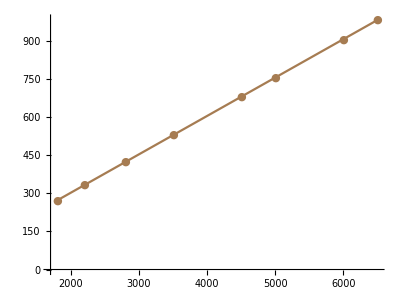

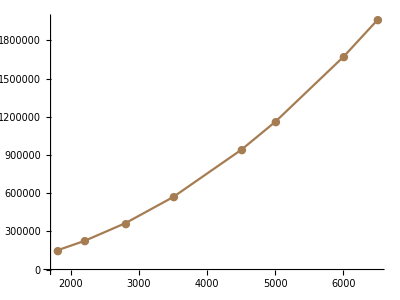

Fraction:{0.7}

C_11: {983.768,908.107,756.787,681.126,529.806,423.882,333.089,272.561}

norm C : {1.96053×10^6,1.67057×10^6,1.16021×10^6,939825.,568627.,363986.,224761.,150498.}

Tempi di calcolo: {83.375,87.0469,87.5781,88.1094,88.0781,88.8281,88.7188,88.1719} in sec

Tempi di calcolo: {1.38958,1.45078,1.45964,1.46849,1.46797,1.48047,1.47865,1.46953} in min

vec

1.22718

```mathematica
(*meshing=0.00001;
meshingbound=0.001;
*)
meshing=0.00001;
meshingbound=0.001;
axR={1};
materialprop={{{6500,0.3},{0.15,0.1}},
			{{6000,0.3},{0.15,0.1}},
			{{5000,0.3},{0.15,0.1}},
			{{4500,0.3},{0.15,0.1}},
			{{3500,0.3},{0.15,0.1}},
			{{2800,0.3},{0.15,0.1}},
			{{2200,0.3},{0.15,0.1}},
			{{1800,0.3},{0.15,0.1}}
			}; 
C11=Table[0*i,{i,1,Length[materialprop]}];
CCC=Table[0*i,{i,1,Length[materialprop]}];
timecalc=Table[0*i,{i,1,Length[materialprop]}];
vec=Table[{0*i,0,j},{i,1,Length[materialprop]},{j,1,2}];
vecandNorm=Table[{0*i,0,j},{i,1,Length[materialprop]},{j,1,2}];
volumefractioncalc=CalcVolFrac[axR];
Do[
timecalc⟦i⟧=Timing[
volfracNew=volumefractioncalc⟦1⟧;
{C11⟦i⟧,CCC⟦i⟧}=Checkconvergence[meshing,meshingbound,False,False,i,axR⟦1⟧,materialprop⟦i⟧];
(*Export[StringJoin[NotebookDirectory[],"test","_mesh_axR_",ToString[materialprop⟦i,1,1⟧],".png"],SMTShowMesh["Mesh"->False,"FillElements"->{RGBColor[0.650,0.486,0.321],RGBColor[0.756,0.152,0.176]}],ImageResolution->300];*)
];
vec⟦i,1⟧=materialprop⟦i,1,1⟧;
vec⟦i,2⟧=C11⟦i⟧;
vecandNorm⟦i,1⟧=materialprop⟦i,1,1⟧;
vecandNorm⟦i,2⟧=CCC⟦i⟧;
,{i,1,Length[materialprop]}]
ListPlot[{vec}, PlotStyle->RGBColor[0.650,0.486,0.321],PlotMarkers->"●",AspectRatio->0.75,Joined->True]
Export[StringJoin[NotebookDirectory[],"graph.pdf"],%];
ListPlot[{vecandNorm}, PlotStyle->RGBColor[0.650,0.486,0.321],PlotMarkers->"●",AspectRatio->0.75,Joined->True]
Print["Fraction:", volumefractioncalc];

Export[StringJoin[NotebookDirectory[],"C11.tex"],Transpose[vec]⟦2⟧];
Print[Subscript["C","11"],": ",Transpose[vec]⟦2⟧];
Export[StringJoin[NotebookDirectory[],"normC.tex"],Transpose[vecandNorm]⟦2⟧];
Print["norm C : ",Transpose[vecandNorm]⟦2⟧];
Print["Tempi di calcolo: ",Transpose[timecalc]⟦1⟧," in sec"];
Print["Tempi di calcolo: ",Transpose[timecalc]⟦1⟧/60," in min"];
(*Checkconvergence[meshdimension,verboseOutput,DebugVal,iteration];*)
```